# Anharmonic Chains

Reference: H. Spohn, Nonlinear fluctuating hydrodynamics for anharmonic chains. J. Stat. Phys. 154, 1191-1227 (2014)

Shoulder potential

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
<<"anharm_chains_shoulder.m";
```

## Import initial data

```mathematica
(* load position data from disk *)
Subscript[r, data,0]=Import["collision_test2_field_r0.dat","Real64"]
```

{0.69521,1.49893,1.7791,1.44995,1.46515,0.671785,1.28999,0.567541,1.81186,1.57329,1.97823,1.19215,1.31328,1.05634,1.45588,1.80052}

```mathematica
(* length L, should be conserved *)
Total[Subscript[r, data,0]]
```

21.5992

```mathematica
Subscript[q, data,0]=Most[Accumulate[Prepend[Subscript[r, data,0],0]]]
Length[%]
```

{0,0.69521,2.19414,3.97325,5.4232,6.88835,7.56013,8.85012,9.41766,11.2295,12.8028,14.781,15.9732,17.2865,18.3428,19.7987}

16

```mathematica
(* load momentum data from disk *)
Subscript[p, data,0]=Import["collision_test2_field_p0.dat","Real64"]
```

{0.510362,0.265417,-0.110275,1.3058,-0.330692,0.34763,-0.60453,-0.310875,0.204896,0.169026,0.0562263,0.780131,0.595775,0.203211,0.223302,0.670621}

```mathematica
(* expectation value is zero, but not current actual value *)
Mean[Subscript[p, data,0]]
```

0.248501

```mathematica
Subscript[V, pot]={1/2,1,1};
```

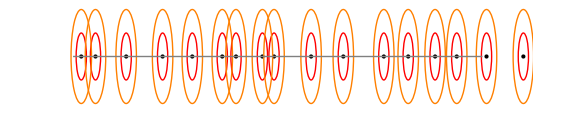

```mathematica
VisualizeField[Accumulate[Prepend[Subscript[r, data,0],0.4]],Subscript[V, pot],20]
```

```mathematica
(* without collision detection *)
Animate[VisualizeField[Subscript[q, data,0]+0.4+t Subscript[p, data,0],Subscript[V, pot],20],{t,0,10},AnimationRunning->False]
```

## Run simulation

```mathematica
(* example *)
NextCollision[Subscript[r, data,0],Subscript[p, data,0],Subscript[V, pot]]
```

{1/2,0.952159,0.180416,Core,6}

```mathematica
(* example *)
CollisionInfo[{Subscript[q, data,0],Subscript[p, data,0],0},Total[Subscript[r, data,0]],Subscript[V, pot]]
```

{0.180416,Core,6,{0.952159,-0.122305}}

```mathematica
(* example *)
UpdateField[{Subscript[q, data,0],Subscript[p, data,0],0},Total[Subscript[r, data,0]],Subscript[V, pot]]
Differences[First[%]]
```

{{0.0920776,0.743096,2.17425,4.20883,5.36353,6.95107,7.45107,8.79404,9.45463,11.26,12.813,14.9218,16.0807,17.3231,18.3831,19.9197},{0.510362,0.265417,-0.110275,1.3058,-0.330692,-0.60453,0.34763,-0.310875,0.204896,0.169026,0.0562263,0.780131,0.595775,0.203211,0.223302,0.670621},0.180416}

{0.651018,1.43115,2.03459,1.1547,1.58753,0.5,1.34297,0.660595,1.80539,1.55294,2.10884,1.15889,1.24245,1.05997,1.53658}

```mathematica
Subscript[f, seq]=FieldSequence[{Subscript[q, data,0],Subscript[p, data,0],0},Total[Subscript[r, data,0]],Subscript[V, pot],52];
Length[%]
```

53

```mathematica
(* example *)
Subscript[f, seq]⟦{1,2,-1}⟧
```

{{{0,0.69521,2.19414,3.97325,5.4232,6.88835,7.56013,8.85012,9.41766,11.2295,12.8028,14.781,15.9732,17.2865,18.3428,19.7987},{0.510362,0.265417,-0.110275,1.3058,-0.330692,0.34763,-0.60453,-0.310875,0.204896,0.169026,0.0562263,0.780131,0.595775,0.203211,0.223302,0.670621},0},{{0.0920776,0.743096,2.17425,4.20883,5.36353,6.95107,7.45107,8.79404,9.45463,11.26,12.813,14.9218,16.0807,17.3231,18.3831,19.9197},{0.510362,0.265417,-0.110275,1.3058,-0.330692,-0.60453,0.34763,-0.310875,0.204896,0.169026,0.0562263,0.780131,0.595775,0.203211,0.223302,0.670621},0.180416},{{0.629641,1.20444,2.73343,3.73343,5.32271,6.45111,7.49636,9.8907,11.0228,13.5217,15.0814,16.2163,18.0794,18.7295,19.7946,20.862},{-0.330692,0.595775,0.265417,0.780131,0.670621,-0.386142,0.510362,0.169026,0.0562263,1.07119,0.203211,0.223302,-0.640284,1.50269,-0.60453,-0.110275},3.91165}}

```mathematica
Interpolation[{Last[#],First[#]}&/@Subscript[f, seq],InterpolationOrder->1]
Animate[VisualizeField[%[t],Subscript[V, pot],20],{t,0,4},AnimationRunning->False]
```

InterpolatingFunction[{{0., 3.91165}}, <>]

## Compare with C implementation

```mathematica
"collision_test2_event_";
Subscript[coll, test]=Transpose[{(* event times *)Import[%<>"time.dat","Real64"],(* event types *) Import[%<>"type.dat","Integer32"]/.{0->PlatIn,1->PlatOut,2->PlatBounce,3->Core},(* particle indices *)Import[%<>"iprt.dat","Integer32"]+1}];
Length[%]
```

53

```mathematica
(* example *)
Subscript[coll, test]⟦{1,2,-1}⟧
```

{{0.180416,Core,6},{0.274949,PlatBounce,4},{3.94256,PlatIn,14}}

```mathematica
Most[CollisionInfo[AdvanceField[#,0.0001],Total[Subscript[r, data,0]],Subscript[V, pot]]]&/@Subscript[f, seq];
(* compare *)
Norm[%-Subscript[coll, test]]
```

2.11583×10^-13

```mathematica
(* reference *)
Subscript[coll, ref]=Most[CollisionInfo[AdvanceField[#,0.0001],Total[Subscript[r, data,0]],Subscript[V, pot]]]&/@Subscript[f, seq];
Length[%]
```

53

```mathematica
(* save to disk for comparison *)
"collision_test2_ref_event_";
{(* event times *)Export[%<>"time.dat",Subscript[coll, ref]⟦;;,1⟧,"Real64"],(* event types *) Export[%<>"type.dat",Subscript[coll, ref]⟦;;,2⟧/.{PlatIn->0,PlatOut->1,PlatBounce->2,Core->3},"Integer32"],(* particle indices *)Export[%<>"iprt.dat",Subscript[coll, ref]⟦;;,3⟧-1,"Integer32"]};
```